The Nonlinear Coupler - fitting the data
Prof. Charlie Ironside
Department of Physics and Astronomy
Curtin University 
Bentley Campus,
Western Australia 6102
email: Charlie.Ironside@curtin.edu.au
web page address:http://oasisapps.curtin.edu.au/staff/profile/view/Charlie.Ironside
Included in the book : “Semiconductor Integrated Optics for Switching Light” by Charlie Ironside 
This note book is based on :-
S. M. Jensen, “THE NON-LINEAR COHERENT COUPLER,” IEEE Journal of Quantum Electronics, vol. 18, pp. 1580-1583, 1982.http://dx.doi.org/10.1109/jqe.1982.1071438
J. S. Aitchison, A. H. Kean, C. N. Ironside, A. Villeneuve, and G. I. Stegeman, “Ultrafast All-Optical Switching in Al0.18ga0.82as Directional Coupler in 1.55 Mu-M Spectral Region,” Electronics Letters, vol. 27, pp. 1709-1710, Sep 12 1991  http://dx.doi.org/10.1049/el:19911064
A. Villeneuve, K. Alhemyari, J. U. Kang, C. N. Ironside, J. S. Aitchison, and G. I. Stegeman, “Demonstration of All-Optical Demultiplexing at 1555nm with an AlGaAs Directional Coupler,” Electronics Letters, vol. 29, pp. 721-722, Apr 15 1993  http://dx.doi.org/10.1049/el:19930482



-Graphics-
We are trying to model this result

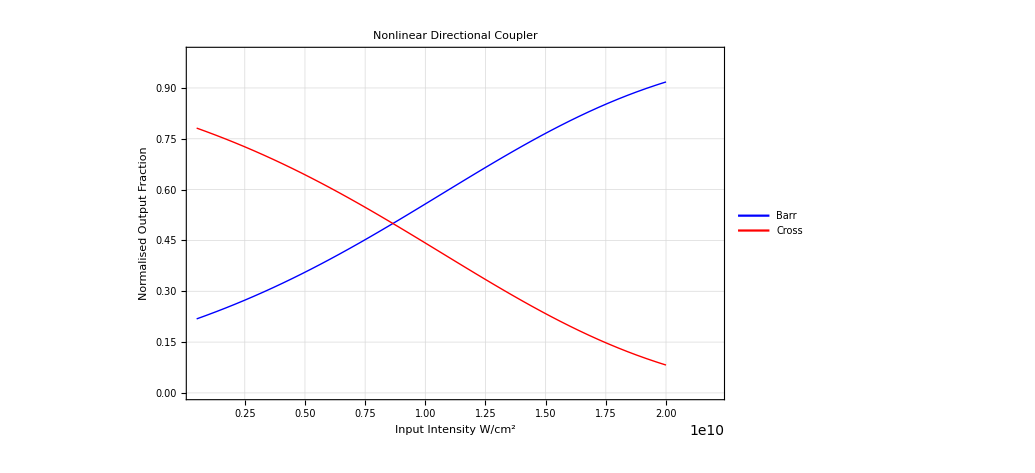

```mathematica
(*Define Design of Nonlinear Coherent coupler*)
ClearAll[Iin]
Lz:= 6.25×10^-3;(* Input Transfer Length, m *)
Lc:=Lz/0.7;
λ=1.6×10^-6;(* Wavelength, m *)
n2:=1.6×10^-14;(* nonlinear refractive index, cm^2 W^-1*)
Ic:=λ/(Lc*n2)
m:=Iin/Ic
Ibarr=(1+JacobiCN[π Lz/Lc,m])/2;
Icross=1-Ibarr;
IinStart:=5.0×10^8
IinFinish:=20.0×10^9
ModelPlot=Plot[{Ibarr,Icross},{Iin,IinStart,IinFinish},PlotRange->{{IinStart,IinFinish*1.1},{0,1}},Frame->True,PlotLabel->"Nonlinear Directional Coupler",AxesStyle->Thin,GridLines->Automatic, PlotStyle->{Directive[Thick,Blue],Directive[Thick,Red]},PlotLegends->Placed[{"Barr","Cross"},{0.5,0.8}],LabelStyle->{FontFamily->"Times New Roman",24,GrayLevel[0]},FrameLabel->{"Input Intensity W/cm^2","Normalised Output Fraction"},FrameStyle->Thick]
```

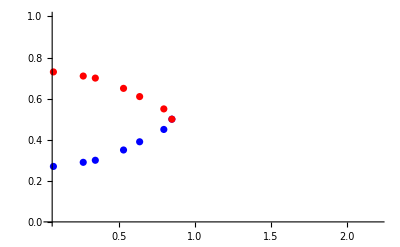

```mathematica
Scaled1:=5.3;(*In the paper the output power is given here we use a scaling factor to estimate the input power - takes account of coupling loss and scattering*) 
DataBarr={{Scaled1*1.3×10^8,0.27},{Scaled1*5×10^8,0.29},{Scaled1*6.5×10^8,0.30},{Scaled1*1.0×10^9,0.35},{Scaled1*1.2×10^9,0.39},{Scaled1*1.5×10^9,0.45},{Scaled1*1.6×10^9,0.5}};DataCross={{Scaled1*1.3×10^8,1-0.27},{Scaled1*5×10^8,1-0.29},{Scaled1*6.5×10^8,1-0.30},{Scaled1*1.0×10^9,1-0.35},{Scaled1*1.2×10^9,1-0.39},{Scaled1*1.5×10^9,1-0.45},{Scaled1*1.6×10^9,1-0.5}};

DataBarrCrossPlot=ListPlot[{DataBarr,DataCross},PlotRange->{{IinStart,IinFinish*1.1},{0,1}},PlotStyle->{Directive[Thick,Blue],Directive[Thick,Red]}]
```

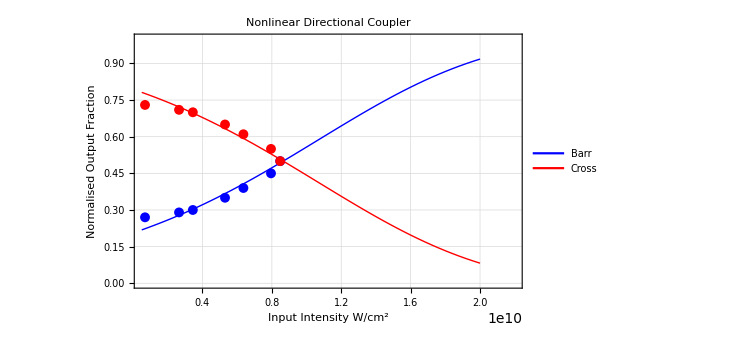

```mathematica
Show[{ModelPlot,DataBarrCrossPlot},PlotRange->{{IinStart,IinFinish*1.1},{0,1}}]
```